-Graphics3D-

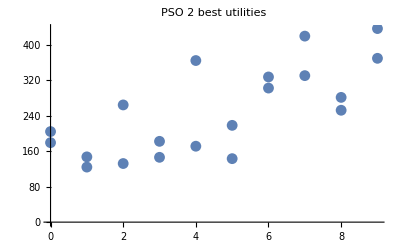

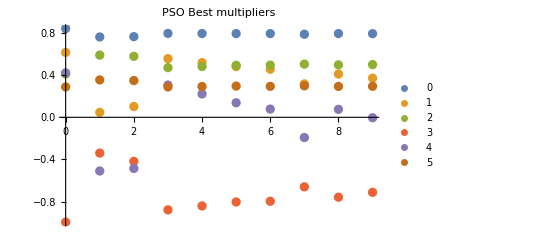

-Graphics3D-

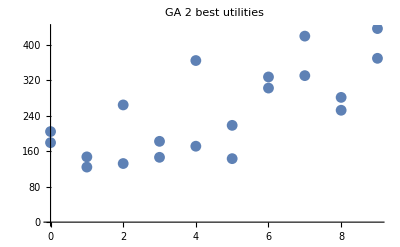

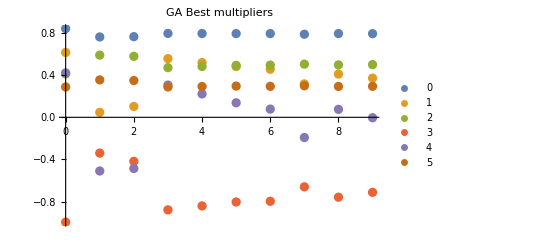

{Null,Null}

```mathematica
algorithms = {"PSO", "GA"};

Table[
ListPointPlot3D[Import[FileNameJoin[{NotebookDirectory[], StringJoin[i,"_allUtilities.log"]}], "Table"], PlotRange-> All, PlotLabel-> StringJoin[i," all utilities"]] // Print
;

ListPlot[Import[FileNameJoin[{NotebookDirectory[], StringJoin[i,"_twoBestUtilities.log"]}], "Table"], PlotLabel -> StringJoin[i," 2 best utilities"]]  // Print

;

in = Import[FileNameJoin[{NotebookDirectory[], StringJoin[i,"_bestMultipliers.log"]}], "Table", FieldSeparators -> { ",", " "}];
ListPlot[Partition[in, Length[in]/6],PlotLegends->{0,1,2,3,4,5},PlotLabel->StringJoin[i," Best multipliers"]] // Print
, {i, algorithms}]
```

-Graphics3D-

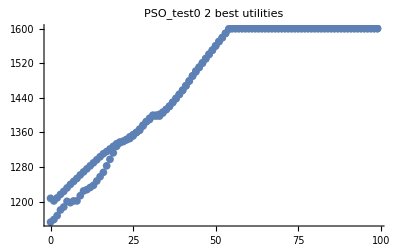

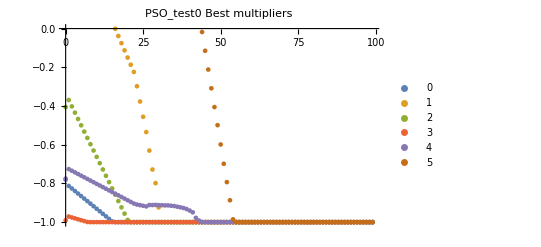

-Graphics3D-

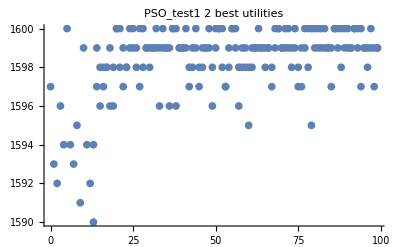

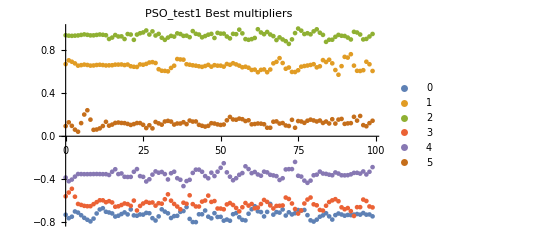

-Graphics3D-

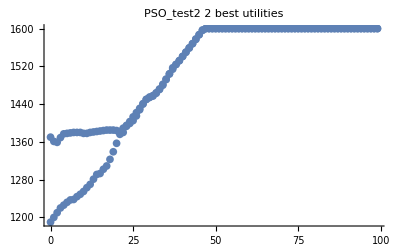

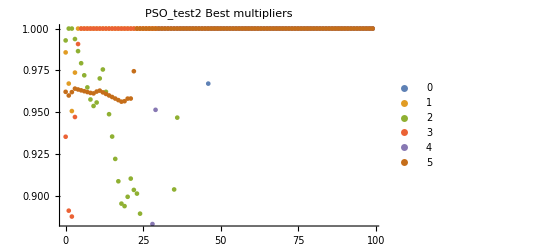

-Graphics3D-

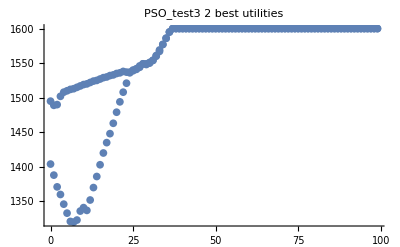

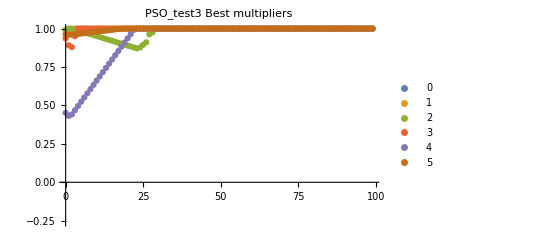

-Graphics3D-

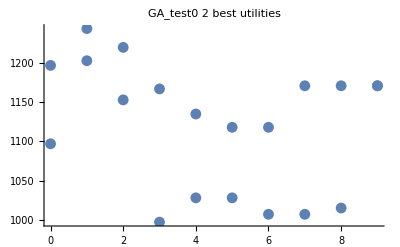

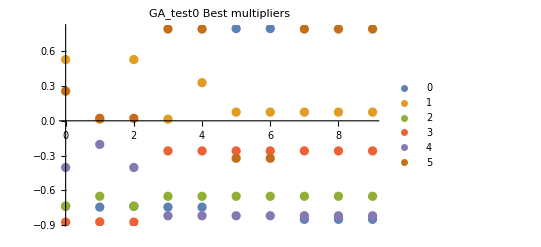

-Graphics3D-

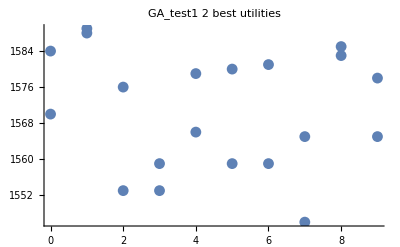

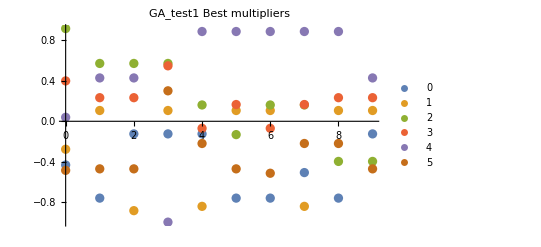

-Graphics3D-

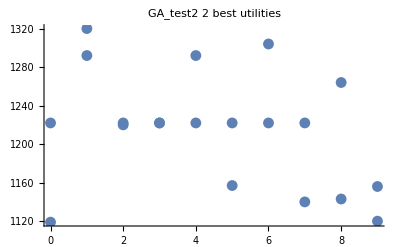

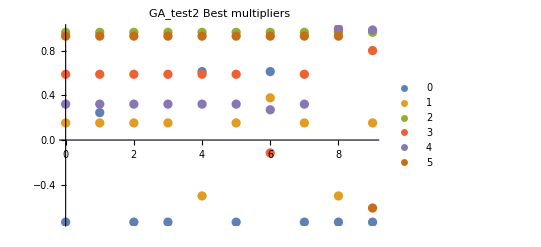

-Graphics3D-

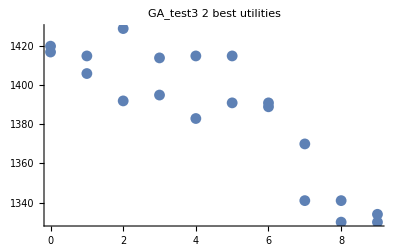

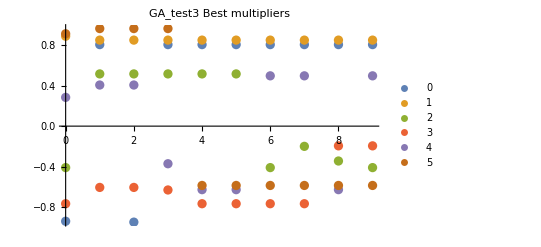

{Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
algorithms = {"PSO_test0", "PSO_test1", "PSO_test2", "PSO_test3", "GA_test0", "GA_test1","GA_test2", "GA_test3"};

Table[
ListPointPlot3D[Import[FileNameJoin[{NotebookDirectory[], StringJoin[i,"_allUtilities.log"]}], "Table"], PlotRange-> All, PlotLabel-> StringJoin[i," all utilities"]] // Print
;

ListPlot[Import[FileNameJoin[{NotebookDirectory[], StringJoin[i,"_twoBestUtilities.log"]}], "Table"], PlotLabel -> StringJoin[i," 2 best utilities"]]  // Print

;

in = Import[FileNameJoin[{NotebookDirectory[], StringJoin[i,"_bestMultipliers.log"]}], "Table", FieldSeparators -> { ",", " "}];
ListPlot[Partition[in, Length[in]/6],PlotLegends->{0,1,2,3,4,5},PlotLabel->StringJoin[i," Best multipliers"]] // Print
, {i, algorithms}]
```